```mathematica
Exit
```

```mathematica
x1=π/2;
δ[r_,a_,α_] = r^2+a^2 + r^4/(32 π α)(1-√(1+(128 π α)/r^3));
σ = r^2+ a^2 Cos[x1]^2;
g11[r_,a_,α_]= -((δ[r,a,α]-a^2 Sin[x1]^2)/σ);
g14[r_,a_,α_] = -a Sin[x1]^2(1-(δ[r,a,α]-a^2 Sin[x1]^2)/σ);
g22[r_,a_,α_] = σ/δ[r,a,α];
g33[r_,a_]=σ;
g44[r_,a_,α_]=Sin[x1]^2(σ+a^2 Sin[x1]^2(2-(δ[r,a,α]-a^2 Sin[x1]^2)/σ));
```

α - GB coupling constant

```mathematica
Limit[δ[r,a,α],{α->0,a->0}]
```

lim_(α→0) lim_(a→0) δ[r,a,α]

## Bh and No bh region

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

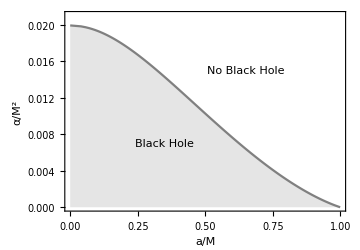

```mathematica
M=1;
Δ=r^2+a^2 + r^4/(32 π l)(1-√(1+(128 π l)/r^3));
rr=Table[a/. FindRoot[ {Δ==0 && D[Δ,r]==0},{r,1},{a,1}],{l,0.000001,0.02,0.0001}];
ll=Table[l,{l,0.000001,0.02,0.0001}];
HH=Table[{rr[[i]],ll[[i]]},{i,Length[ll]}];
ListLinePlot[HH,
PlotRange->{{0,1},{0,0.021}},
PlotStyle->{Gray},
FrameLabel->{"a/M","α/M^2"},
Frame->True,
FrameStyle->Black,
AspectRatio->0.7,ImageSize->Medium,Filling->Axis,
BaseStyle->{11.5,FontFamily->"Times",Italic,Bold},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.35,0.007}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.65,0.015}]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

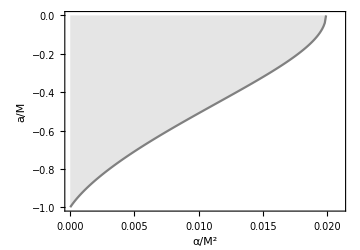

```mathematica
rr=Table[a/. FindRoot[ {Δ==0 && D[Δ,r]==0},{r,1},{a,-0.995}],{l,0.000001,0.02,0.0001}];
ll=Table[l,{l,0.000001,0.02,0.0001}];
HH1=Table[{ll[[i]],rr[[i]]},{i,Length[ll]}];
ListLinePlot[HH1,
PlotRange->{{0,0.021},{0,-1}},
PlotStyle->{Gray},
FrameLabel->{"α/M^2","a/M"},
Frame->True,
FrameStyle->Black,
AspectRatio->0.7,ImageSize->Medium,Filling->Axis,
BaseStyle->{13,FontFamily->"TimesNewRoman"},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.35,0.007}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.65,0.015}]}]
```

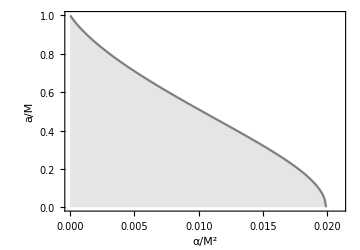
```mathematica
tik11=-Graphics-;
```

```mathematica
tik12=-Graphics-;
```

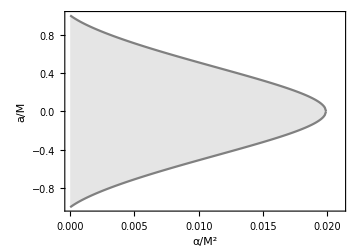

```mathematica
tik1=Show[tik11,tik12,PlotRange->{{0.000001,0.021},{-1,1}},Frame->True]
```

## Horizon

```mathematica
Limit[δ[r,a,α],α-> 0]
```

a^2+(-2+r) r

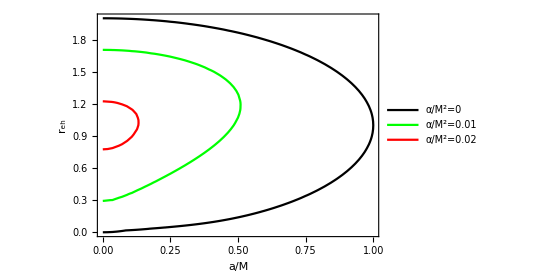

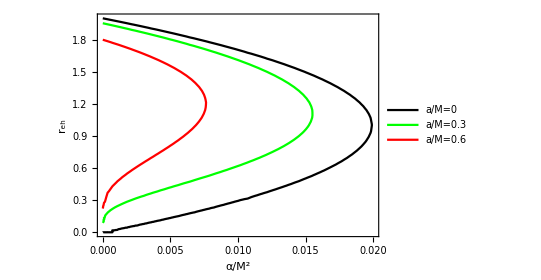

time: 28940.05915

```mathematica
ContourPlot[{δ[r,a,0.000001](*Black*)==0,δ[r,a,0.01](*Green*)==0,δ[r,a,0.0188885](*Red*)==0},{a,0,1},{r,0,2},ContourStyle->{Black,Green,Red},PlotLegends->Placed[{"α/M^2=0","α/M^2=0.01","α/M^2=0.02"},{Scaled[{0.7,0.54}],{0.5,0.5}}],Frame->True,FrameLabel->{"a/M","r_eh"},BaseStyle->{15,FontFamily->"TimesNewRoman"},FrameStyle->Black,AspectRatio->0.7,LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5}]

ContourPlot[{δ[r,0,α](*Black*)==0,δ[r,0.3,α](*Green*)==0,δ[r,0.6,α](*Red*)==0},{α,10^-5,0.02},{r,0,2},ContourStyle->{Black,Green,Red},PlotLegends->Placed[{"a/M=0","a/M=0.3","a/M=0.6"},{Scaled[{0.17,0.6}],{0.5,0.5}}],Frame->True,FrameLabel->{"α/M^2","r_eh"},BaseStyle->{15,FontFamily->"TimesNewRoman"},FrameStyle->Black,AspectRatio->0.7,LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5}]
t = SessionTime[];
Print["time: ",t]
```

## Effective potential

```mathematica
Veff[r_,a_,α_,Ene_,L_]= (Ene^2 g44[r,a,α] + 2 Ene L g14[r,a,α]+L^2 g11[r,a,α])/(g14[r,a,α]^2 - g11[r,a,α] g44[r,a,α])-1;
```

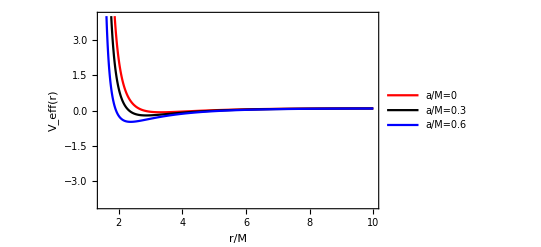

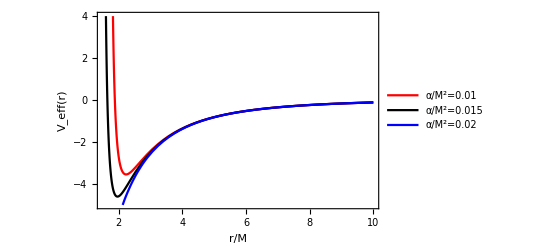

```mathematica
Plot[{Veff[r,0.,0.015,1,4],Veff[r,0.1,0.015,1,4],Veff[r,0.2,0.015,1,4]},{r,1.5,10},Frame->True,FrameLabel->{"r/M","V_eff(r)","ℒ=6, α/M^2 = 0.015"},PlotStyle->{Red,Black,Blue},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"a/M=0","a/M=0.3","a/M=0.6"},{Scaled[{0.75,0.25}],{0.5,0.5}}],PlotRange->{{1.5,10}, {-4, 4}}]

Plot[{Veff[r,0.1,0.01,1,6],Veff[r,0.1,0.015,1,6],Veff[r,0.1,0.02,1,6]},{r,1.5,10},Frame->True,FrameLabel->{"r/M","V_eff(r)","ℒ=6, a/M = 0.1"},PlotStyle->{Red,Black,Blue},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"α/M^2=0.01","α/M^2=0.015","α/M^2=0.02"},{Scaled[{0.75,0.25}],{0.5,0.5}}],PlotRange->{{1.5,10}, {-5, 4}}]
```

## Isco radii

```mathematica
ω=1/D[g44[r,a,α], r](-D[g14[r,a,α], r] + √((D[g14[r,a,α], r])^2-(D[g11[r,a,α], r]) (D[g44[r,a,α], r])));
```

```mathematica
tdot = 1/(√(-g11[r,a,α]-2 ω g14[r,a,α] - ω^2 g44[r,a,α]));
```

```mathematica
L[r_,a_,α_] = (g14[r,a,α] + ω g44[r,a,α]) tdot;
```

```mathematica
Lp[r_,a_,α_] = D[L[r,a,α],r];
```

```mathematica
RedDashed[a,r]= If[r≥2.846,Lp[r,a,0.02],None];
BlueDashed[a,r]=If[r≥2.243,Lp[r,a,0.01],None];
```

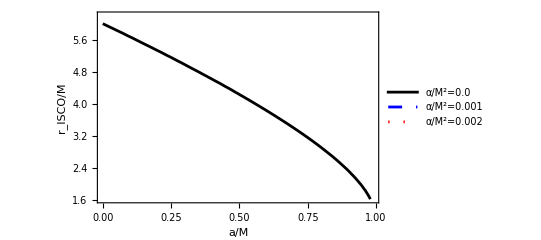

```mathematica
ContourPlot[{Lp[r,a,10^-6]==0,BlueDashed[a,r]==0,RedDashed[a,r]==0},{a,0,1},{r,1.62343,6},Frame->True,FrameLabel->{"a/M","r_ISCO/M"},ContourStyle->{{Black},{Dashed,Blue},{Dotted,Red}},AspectRatio->0.6,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotRange->{{0,0.99},{1.62343,6.2}},PlotLegends->Placed[{"α/M^2=0.0","α/M^2=0.001","α/M^2=0.002","α/M^2=0.01","α/M^2=0.02"},{Scaled[{0.550,0.7}],{0,0.5}}]]
```

```mathematica
Fr[α,r]=If[r>=2.868,Lp[r,0.298,α],None];
```

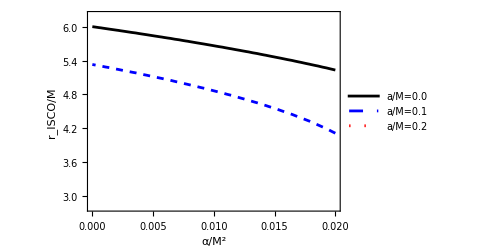

```mathematica
ContourPlot[{Lp[r,0,α]==0,Lp[r,0.2,α]==0,Fr[α,r]==0},{α,10^-6,0.02},{r,2.8,6.2},Frame->True,FrameLabel->{"α/M^2","r_ISCO/M"},ContourStyle->{{Black},{Dashed,Blue},{Dotted,Red}},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"a/M=0.0","a/M=0.1","a/M=0.2","a/M=0.3","a/M=0.6"},{Scaled[{0.2,0.21}],{0,0.5}}],ImageSize->Medium]
```

## radiative efficiency

```mathematica
Lp[r_,a_,α_] = D[L[r,a,α],r];
Ene[r_,a_,α_] = -(g11[r,a,α]+ω*g14[r,a,α])*tdot;
```

```mathematica
rr1[a_,α_] := r/.FindRoot[Lp[r,a,α]==0,{r,6}]                     (*ISCO*)
```

```mathematica
rr1[0.,10^-5]
```

5.99969

```mathematica
(*rr2[a_,α_] := y/.FindRoot[Lp[y,a,α]==0,{y,6}];*)
```

```mathematica
(*rr3[a_,α_] := z/.FindRoot[Lp[z,a,α]==0,{z,6}];*)
```

```mathematica
rr1[0.,10^-9]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

6.

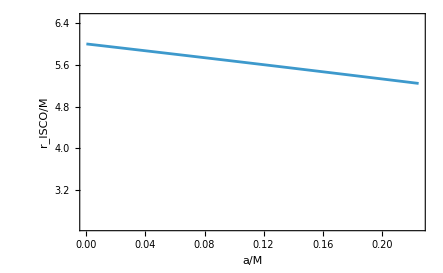

```mathematica
Plot[rr1[a,0.00001],{a,0,0.225},PlotRange->{2.5,6.5},Frame->True,FrameLabel->{"a/M","r_ISCO/M"}]
```

```mathematica
5
```

5

```mathematica
η[a_,α_] := 1- Ene[rr1[a,α],a,α];
```

```mathematica
(*η2[a_,α_] := 1-Ene[rr2[a,α],a,α];*)
```

```mathematica
(*η3[a_,α_] := 1-Ene[rr3[a,α],a,α];*)
```

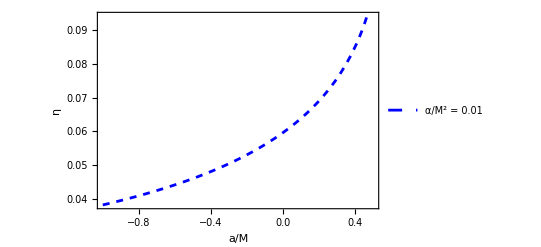

```mathematica
p1=Plot[η[a,0.01],{a,-1,0.499237542},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Dashed,Blue},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"α/M^2 = 0.01"},{Scaled[{0.05,0.8}],{0,0.5}}]]
```

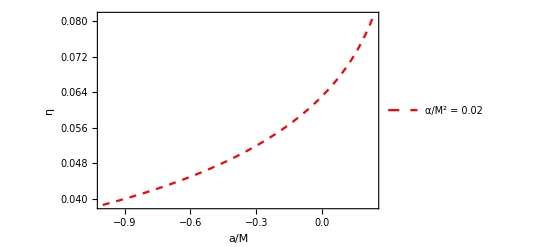

```mathematica
p2=Plot[η[a,0.02],{a,-0.9996,0.234},Frame->True,FrameLabel->{"a/M","η"},PlotStyle->{Dashed,Red},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"α/M^2 = 0.02"},{Scaled[{0.05,0.9}],{0,0.5}}]]
```

```mathematica
η[1,10^-6]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.000112134

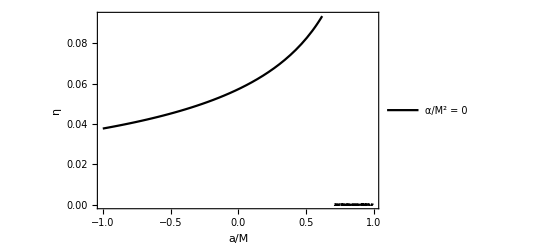

```mathematica
p3=Plot[η[a,10^-6],{a,-1,0.996934},Frame->True,FrameLabel->{"a/M","η"},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 15},PlotStyle->Black,PlotLegends->Placed[{"α/M^2 = 0"},{Scaled[{0.05,0.7}],{0,0.5}}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

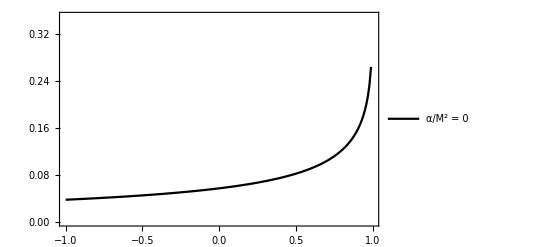

```mathematica
f1:=ListLinePlot[Table[{a,1-Ene[r, a, 10^-6]/.FindRoot[Lp[r, a, 0.00000000001]==0,{r,7}]},{a,-1,0,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,PlotStyle->{Black},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];
f2:=ListLinePlot[Table[{a,1-Ene[r, a, 0.00000000001]/.FindRoot[Lp[r, a, 0.00000000001]==0,{r,3}]},{a,0,0.92,0.01}],PlotRange->{{0, 1}{0, 0.4}}, Frame->True,PlotLegends->Placed[{"α/M^2 = 0"},{Scaled[{0.13,0.9}], {0.4, 0.5}}],PlotStyle->{Black},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];
f3:=ListLinePlot[Table[{a,1-Ene[r, a, 0.00000000001]/.FindRoot[Lp[r, a, 0.00000000001]==0,{r,1.5}]},{a,0.92,0.999,0.01}], PlotRange->{{0, 1}{0, 0.4}},Frame->True,PlotStyle->{Black},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

F1=Show[f1,f2,f3,PlotRange->{{-1,1},{0,0.35}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]
```

```mathematica
Clear[f1,f2,f3,F1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

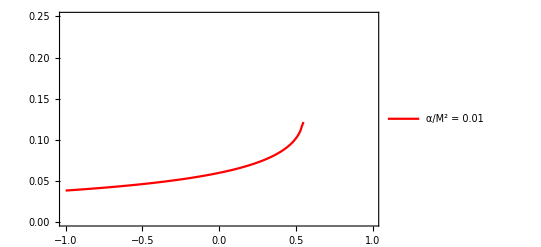

```mathematica
f1:=ListLinePlot[Table[{a,1-Ene[r, a, 0.01]/.FindRoot[Lp[r, a, 0.01]==0,{r,7}]},{a,-1,0,0.01}], PlotRange->{{0, 1}{0, 0.35}},Frame->True,PlotStyle->{Red},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]

f2:=ListLinePlot[Table[{a,1-Ene[r, a, 0.01]/.FindRoot[Lp[r, a, 0.01]==0,{r,3.5}]},{a,0,0.55,0.01}],PlotRange->{{0, 1}{0, 0.35}}, Frame->True,PlotLegends->Placed[{"α/M^2 = 0.01"},{Scaled[{0.16,0.75}], {0.4, 0.5}}],PlotStyle->{Red},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]

f3:=ListLinePlot[Table[{a,1-Ene[r, a, 0.01]/.FindRoot[Lp[r, a, 0.01]==0,{r,1.01}]},{a,0.55,0.6,0.01}], PlotRange->{{0, 1}{0, 0.35}},Frame->True,PlotStyle->{Red},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]

(*f4=ListLinePlot[Table[{a,1-Ene[r, a, 0.01]/.FindRoot[Lp[r, a, 0.01]==0,{r,5}]},{a,0.82,0.85,0.01}], PlotRange->{{0, 1}{0, 0.35}},Frame->True,PlotStyle->{Red, Dashed}]*)
F2=Show[f1,f2,PlotRange->{{-1,1},{0,0.25}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]
```

```mathematica
Clear[f1,f2,f3]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

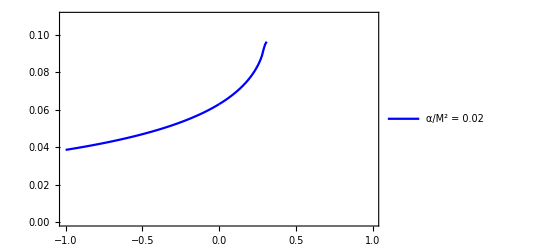

```mathematica
f1:=ListLinePlot[Table[{a,1-Ene[r, a, 0.02]/.FindRoot[Lp[r, a, 0.02]==0,{r,7}]},{a,-1,0,0.01}], PlotRange->{{0, 1}{0, 0.11}},Frame->True,PlotStyle->{Blue},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]

f2:=ListLinePlot[Table[{a,1-Ene[r, a, 0.02]/.FindRoot[Lp[r, a, 0.02]==0,{r,3.5}]},{a,0,0.31,0.01}],PlotRange->{{0, 1}{0, 0.11}}, Frame->True,PlotLegends->Placed[{"α/M^2 = 0.02"},{Scaled[{0.16,0.6}], {0.4, 0.5}}],PlotStyle->{Blue},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]

f3=ListLinePlot[Table[{a,1-Ene[r, a, 0.02]/.FindRoot[Lp[r, a, 0.02]==0,{r,3}]},{a,0.307,0.32,0.01}], PlotRange->{{0, 1}{0, 0.11}},Frame->True,PlotStyle->{Blue},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}];

(*f4=ListLinePlot[Table[{a,1-Ene[r, a, 0.01]/.FindRoot[Lp[r, a, 0.01]==0,{r,5}]},{a,0.82,0.85,0.01}], PlotRange->{{0, 1}{0, 0.35}},Frame->True,PlotStyle->{Red, Dashed}]*)
F3=Show[f1,f2,PlotRange->{{-1,1},{0,0.11}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 11.5}]
```

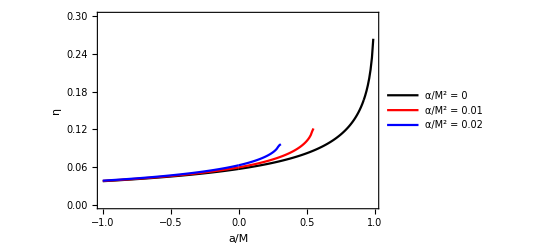

```mathematica
Show[F1,F2,F3,PlotRange->{0,0.3},FrameLabel->{"a/M", "η"},RotateLabel->True,LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5}]
```

```mathematica
dd1=ParallelTable[{α,η[0.01,α]},{α,10^-6,0.023,0.001}]
dd2=ParallelTable[{α,η[0.15,α]},{α,10^-6,0.02,0.001}];
dd3=ParallelTable[{α,η[0.35,α]},{α,10^-6,0.0169,0.001}];
dd4=ParallelTable[{α,η[0.45,α]},{α,10^-6,0.01,0.001}];
```

CloudConnect::verr: This version of Mathematica is no longer supported for use with the Wolfram Cloud beginning Wed 1 Jan 2025. Please

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{1.×10^-6,0.0575141},{0.001001,0.0577415},{0.002001,0.0579742},{0.003001,0.0582127},{0.004001,0.0584571},{0.005001,0.0587078},{0.006001,0.0589651},{0.007001,0.0592294},{0.008001,0.059501},{0.009001,0.0597805},{0.010001,0.0600683},{0.011001,0.0603649},{0.012001,0.0606709},{0.013001,0.0609869},{0.014001,0.0613136},{0.015001,0.0616518},{0.016001,0.0620024},{0.017001,0.0623665},{0.018001,0.062745},{0.019001,0.0631393},{0.020001,0.0635509},{0.021001,0.0639814},{0.022001,0.0644329}}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

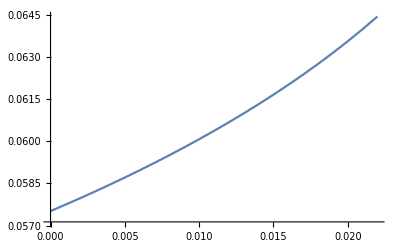

```mathematica
ListLinePlot[dd1]
```

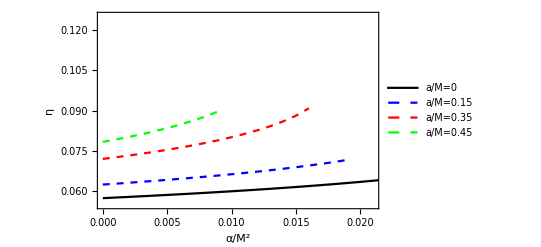

```mathematica
ListLinePlot[{dd1,dd2,dd3,dd4},PlotStyle->{Black,{Dashed,Blue},{Dashed,Red},{Dashed,Green}},PlotRange->{{0,0.021},{0.055,0.125}},Frame->True,FrameLabel->{"α/M^2","η"},LabelStyle->{FontFamily -> "Times",Black, Italic,Bold,FontSize-> 11.5},PlotLegends->Placed[{"a/M=0","a/M=0.15","a/M=0.35","a/M=0.45"},{Scaled[{0.015,0.999}],{0.03,0.98}}]]
```

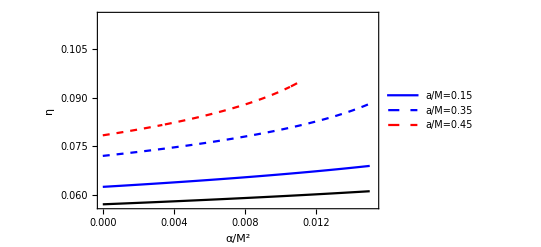

```mathematica
Plot[{ η[0.15,α],η[0.35,α],η[0.45,α],η[0.,α]},{α,10^-9,0.015},PlotStyle->{Blue,{Dashed,Blue},{Dashed,Red},Black},Frame->True,FrameLabel->{"α/M^2","η"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"a/M=0.15","a/M=0.35","a/M=0.45"},{Scaled[{0.03,0.98}],{0.03,0.98}}],PlotRange->{{0,0.0152},{0.057,0.115}}]
```

## Jet

```mathematica
Series[r^2+a^2 + r^4/(32 π α)(1-√(1+(128 π α)/r^3)),{α,0,2}]//Normal
```

a^2-2 r+r^2+(64 π α)/r^2-(4096 π^2 α^2)/r^5

```mathematica
solhor[a_,α_]=Solve[a^2-2 r+r^2+(64 π α)/r^2-(4096 π^2 α^2)/r^5==0,r][[1]];
```

```mathematica
solhor[0.,0.0000001]
```

{r→2.}

```mathematica
rh[a_,α_] := r/.FindRoot[r^2+a^2 + r^4/(32 π α)(1-√(1+(128 π α)/r^3))==0,{r,1.5}];
```

```mathematica
Wh[a_,α_]:=(-g14[r,a,α])/g44[r,a,α]/.{r->rh[a,α]}
```

```mathematica
Wh[0.2,0.01]
```

0.0710854

```mathematica
Clear[dat1,dat2,dat3];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

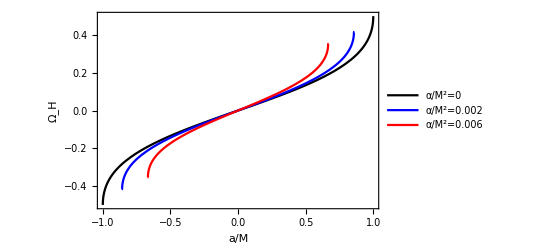

```mathematica
w1[a_]=If[-0.86≤a≤0.86,Wh[a,0.002],None];
w2[a_]=If[-0.67≤a≤0.67,Wh[a,0.006],None];
Plot[{Wh[a,10^-6],w1[a],w2[a]},{a,-1,1},Frame->True,FrameLabel->{"a/M","Ω_H"},PlotLegends->Placed[{"α/M^2=0","α/M^2=0.002","α/M^2=0.006"},{Scaled[{0.5,0.2}],{-0.2,0.4}}],PlotStyle->{Black, Blue,Red},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

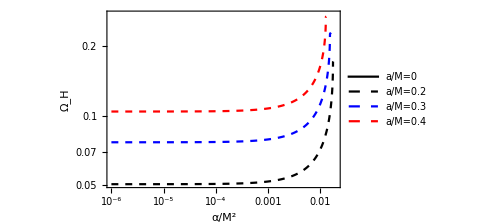

```mathematica
w1[α_]=If[α<=0.0132,Wh[0.4,α],None];(*redDashed*)
w2[α_]=If[α<=0.0162,Wh[0.3,α],None];(*blueDashed*)
w3[α_]=If[α<=0.0179,Wh[0.2,α],None];(*blackDashed*)
LogLogPlot[{Wh[0.,α],w3[α],w2[α],w1[α]},{α,10^-6,0.02},Frame->True,FrameLabel->{"α/M^2","Ω_H"},PlotLegends->Placed[{"a/M=0","a/M=0.2","a/M=0.3","a/M=0.4"},{Scaled[{0.1,0.7}],{-0.2,0.4}}],PlotStyle->{Black,{Dashed,Black},{Dashed,Blue},{Dashed,Red}},LabelStyle->{FontFamily->"Times",Black,Bold,Italic},ImageSize->Medium,PlotRange->{{10^-6,0.02},{-0.01,0.275}}]
```

```mathematica
rp= 1 + √(1-16 π α);
w[α_,a_]=(32 π α a)/(rp^4 (-1 + (1+ (128 π α)/rp^3)^0.5));
```

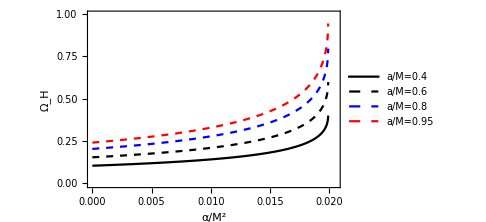

```mathematica
Plot[{w[α,0.4],w[α,0.6],w[α,0.8],w[α,0.95]},{α,10^-6,0.02},Frame->True,FrameLabel->{"α/M^2","Ω_H"},PlotLegends->Placed[{"a/M=0.4","a/M=0.6","a/M=0.8","a/M=0.95"},{Scaled[{0.1,0.62}],{-0.2,0.4}}],PlotStyle->{Black,{Dashed,Black},{Dashed,Blue},{Dashed,Red}},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Medium,PlotRange->{{10^-6,0.0205},{-0.01,1}}]
```

```mathematica
LogK2min = Log[10](2.94-0.22); LogK2 =Log[10]( 2.94); LogK2max = Log[10](2.94+0.22);
LogK5min = Log[10](4.19-0.22);LogK5 =Log[10]( 4.19); LogK5max = Log[10](4.19+0.22);
```

```mathematica
K2min=10^2.72
```

524.807

```mathematica
Sqrt[70/K2min]
```

0.365215

```mathematica
0.36521534778460124 (*!!!*)
```

0.365215

```mathematica
α=0.01
```

0.01

```mathematica
Wh[0.7975440790847127,0.013]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.333822

## A0620-00 (jet)

```mathematica
P2=0.13; P5=1.6;
```

```mathematica
a2min[α_] := a/.FindRoot[Log[P2]==LogK2min + 2 Log[Wh[a,α]],{a,0.04}]//Quiet
a2[α_] := a/.FindRoot[Log[P2]==LogK2 + 2 Log[Wh[a,α]],{a,0.04}]//Quiet
a2max[α_] := a/.FindRoot[Log[P2]==LogK2max + 2 Log[Wh[a,α]],{a,0.04}]//Quiet

a5min[α_] := a/.FindRoot[Log[P5]==LogK5min + 2 Log[Wh[a,α]],{a,0.04}]//Quiet
a5[α_] := a/.FindRoot[Log[P5]==LogK5 + 2 Log[Wh[a,α]],{a,0.04}]//Quiet
a5max[α_] := a/.FindRoot[Log[P5]==LogK5max + 2 Log[Wh[a,α]],{a,0.04}]//Quiet

data2min=ParallelTable[{l, a2min[l]}, {l, 10^-7,0.02, 0.0002}];
data2=ParallelTable[{l, a2[l]}, {l, 10^-7,0.02, 0.0002}];
data2max=ParallelTable[{l, a2max[l]}, {l, 10^-7,0.02, 0.0002}];

data5min=ParallelTable[{l, a5min[l]}, {l, 10^-7,0.02, 0.0002}];
data5=ParallelTable[{l, a5[l]}, {l, 10^-7,0.02, 0.0002}];
data5max=ParallelTable[{l, a5max[l]}, {l, 10^-7,0.02, 0.0002}];
```

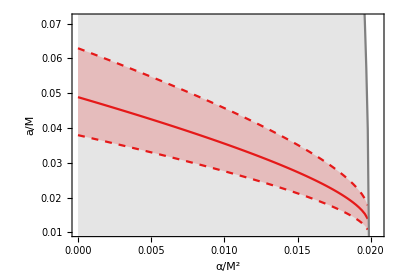

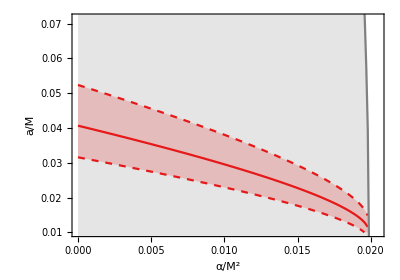

```mathematica
p1=ListPlot[{data2min,data2,data2max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,0.0205},{0.01,0.0715}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
p2=ListPlot[{data5min,data5,data5max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,0.0205},{0.01,0.0715}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
Show[p1,tik1,FrameLabel->{"α/M^2","a/M","Γ = 2","A0620 - 00"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[p2,tik1,FrameLabel->{"α/M^2","a/M","Γ = 5","A0620-00"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## H1743-322

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
Clear[P2,P5]
```

```mathematica
P2=7;P5=140;
```

```mathematica
A2min[α_] := a/.FindRoot[Log[P2]==LogK2min + 2 Log[Wh[a,α]],{a,-13.75 α + 0.44}]//Quiet
A2[α_] := a/.FindRoot[Log[P2]==LogK2 + 2 Log[Wh[a,α]],{a,-11.6 α + 0.352}]//Quiet
A2max[α_] := a/.FindRoot[Log[P2]==LogK2max + 2 Log[Wh[a,α]],{a,-9.63 √(α^2.6) + 0.272}]//Quiet
A5min[α_] := a/.FindRoot[Log[P5]==LogK5min + 2 Log[Wh[a,α]],{a,-1.42 α + 0.46}]//Quiet
A5[α_] := a/.FindRoot[Log[P5]==LogK5 + 2 Log[Wh[a,α]],{a,-10.1 α + 0.36}]//Quiet
A5max[α_] := a/.FindRoot[Log[P5]==LogK5max + 2 Log[Wh[a,α]],{a,-9.55 α + 0.289}]//Quiet
```

```mathematica
Abs[A2max[0.0199]]
```

0.0691666

```mathematica
Data2min=ParallelTable[{l, A2min[l]}, {l, 10^-7,0.02, 0.00135}];
Data2=ParallelTable[{l, A2[l]}, {l, 10^-7,0.02, 0.001}];
Data2max=ParallelTable[{l, A2max[l]}, {l, 10^-7,0.023, 0.0015}];
```

```mathematica
A5max[0.02];
```

```mathematica
Data5min=ParallelTable[{l, A5min[l]}, {l, 10^-6,0.0183, 0.0013}];
Data5max=ParallelTable[{l, A5max[l]}, {l, 10^-6,0.021, 0.0014}];
Data5=ParallelTable[{l, A5[l]}, {l, 10^-6,0.0196, 0.00135}];
```

```mathematica
Clear[f1,f2,d5minModified,d2minModified]
```

```mathematica
αc=0.0184;
d5minModified = Join[Select[Data5min,First[#]≤αc&],Select[(*d5minAlt*)HH,First[#]>αc&]];
```

```mathematica
f1=ListLinePlot[{d5minModified,Data5,Data5max},PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Axes->False,LabelStyle->Directive[Black,Bold],Frame->True,FrameLabel->{"α/M^2","a/M","Γ=5","H1743-322"},Filling->{1->{3}},PlotRange->{{10^-6,0.02},{0.019,0.85}}];
```

```mathematica
αc=0.01884;
d2minModified = Join[Select[Data2min,First[#]≤αc&],Select[(*d5minAlt*)HH,First[#]>αc&]];
```

```mathematica
f2=ListLinePlot[{d2minModified,Data2,Data2max},  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold],FrameLabel->{"α/M^2","a/M","Γ=5","H1743-322","Γ=2"},PlotRange->{{10^-6,0.02},{0.019,0.85}}];
```

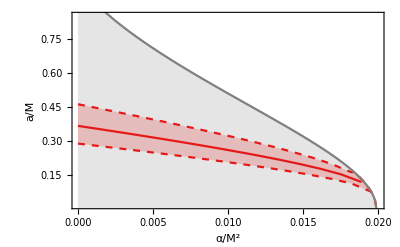

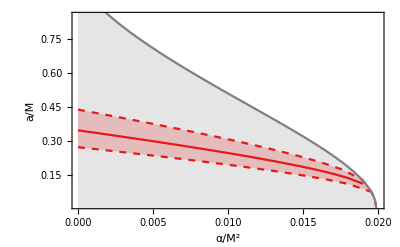

```mathematica
Show[f1,tik1,FrameLabel->{"α/M^2","a/M","Γ = 5","H1743-322"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[f2,tik1,FrameLabel->{"α/M^2","a/M","Γ = 2","H1743-322"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## XTEJ1550-564

```mathematica
Clear[pow1,pow2]
```

```mathematica
pow2=11;pow5=180;
```

```mathematica
aa2min[α_] := a/.FindRoot[Log[pow2]==LogK2min + 2 Log[Wh[a,α]],{a,-19.89 α + 0.54}]//Quiet
aa2[α_] := a/.FindRoot[Log[pow2]==LogK2 + 2 Log[Wh[a,α]],{a,-14 α + 0.429}]//Quiet
aa2max[α_] := a/.FindRoot[Log[pow2]==LogK2max + 2 Log[Wh[a,α]],{a,-11.5 α + 0.334}]//Quiet
aa5min[α_] := a/.FindRoot[Log[pow5]==LogK5min + 2 Log[Wh[a,α]],{a,0.3}]//Quiet
aa5[α_] := a/.FindRoot[Log[pow5]==LogK5 + 2 Log[Wh[a,α]],{a,0.3}]//Quiet
aa5max[α_] := a/.FindRoot[Log[pow5]==LogK5max + 2 Log[Wh[a,α]],{a,-10.79 α + 0.326}]//Quiet
```

```mathematica
aa2min[10^-6]
```

0.534291

```mathematica
Data2min=ParallelTable[{l, aa2min[l]}, {l, 10^-7,0.0181, 0.0015}];
Data2=ParallelTable[{l, aa2[l]}, {l, 10^-7,0.01955, 0.00135}];
Data2max=ParallelTable[{l, aa2max[l]}, {l, 10^-7,0.0199, 0.001355}];
```

```mathematica
Data5min=ParallelTable[{l, aa5min[l]}, {l, 10^-7,0.019, 0.0015}];
Data5=ParallelTable[{l, aa5[l]}, {l, 10^-7,0.01945, 0.00135}];
Data5max=ParallelTable[{l, aa5max[l]}, {l, 10^-7,0.02, 0.0015}];
```

```mathematica
Clear[d2minModified,d5minModified]
```

```mathematica
αc=0.0179;
d2minModified = Join[Select[Data2min,First[#]≤αc&],Select[(*d5minAlt*)HH,First[#]>αc&]];
```

```mathematica
f1=ListLinePlot[{d2minModified,Data2,Data2max},PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Axes->False,LabelStyle->Directive[Black,Bold],Frame->True,FrameLabel->{"α/M^2","a/M","Γ=2","XTEJ1550-564"},Filling->{1->{3}},PlotRange->{{10^-6,0.02},{0.01,0.9955}}];
```

```mathematica
αc=0.01802;
d5minModified = Join[Select[Data5min,First[#]≤αc&],Select[(*d5minAlt*)HH,First[#]>αc&]];
```

```mathematica
f2=ListLinePlot[{d5minModified,Data5,Data5max},PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Axes->False,LabelStyle->Directive[Black,Bold],Frame->True,FrameLabel->{"α/M^2","a/M","Γ=5","XTEJ1550-564"},Filling->{1->{3}},PlotRange->{{10^-6,0.02},{0.05,0.55}}];
```

```mathematica
(*q1=Plot[{aa2min[x],aa2[x],aa2max[x]},{x,10^-6,0.019},Filling->{1->{3}},PlotStyle->{{Dashed,Red},Red,{Dashed,Red}},LabelStyle->Directive[Black,Bold],Frame->True,FrameLabel->{"α/M^2","a/M","XTEJ1550-564","Γ=2"}];*)
```

```mathematica
(*q2=Plot[{aa5min[x],aa5[x],aa5max[x]},{x,10^-6,0.016},Filling->{1->{3}},PlotStyle->{{Dashed,Red},Red,{Dashed,Red}},LabelStyle->Directive[Black,Bold],Frame->True,FrameLabel->{"α/M^2","a/M","XTEJ1550-564","Γ=5"}];*)
```

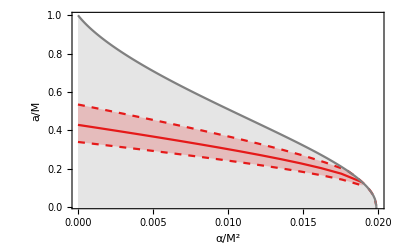

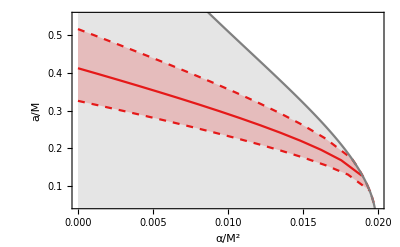

```mathematica
Show[f1,tik1,FrameLabel->{"α/M^2","a/M","Γ = 2","XTEJ1550-564"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[f2,tik1,FrameLabel->{"α/M^2","a/M","Γ = 5","XTEJ1550-564"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## GRS1124-683

```mathematica
Pow2=3.9;Pow5=380;
```

```mathematica
Aa2min[α_] := a/.FindRoot[Log[Pow2]==LogK2min + 2 Log[Wh[a,α]],{a,0.3}]//Quiet
Aa2[α_] := a/.FindRoot[Log[Pow2]==LogK2 + 2 Log[Wh[a,α]],{a,0.3}]//Quiet
Aa2max[α_] := a/.FindRoot[Log[Pow2]==LogK2max + 2 Log[Wh[a,α]],{a,0.3}]//Quiet
Aa5min[α_] := a/.FindRoot[Log[Pow5]==LogK5min + 2 Log[Wh[a,α]],{a,-26.1875 α + 0.695}]//Quiet
Aa5[α_] := a/.FindRoot[Log[Pow5]==LogK5 + 2 Log[Wh[a,α]],{a,-20.54 α + 0.575}]//Quiet
Aa5max[α_] := a/.FindRoot[Log[Pow5]==LogK5max + 2 Log[Wh[a,α]],{a,0.3}]//Quiet
```

```mathematica
Data2min=ParallelTable[{l, Aa2min[l]}, {l, 10^-7,0.023, 0.0015}];
Data2=ParallelTable[{l, Aa2[l]}, {l, 10^-7,0.023, 0.0015}];
Data2max=ParallelTable[{l, Aa2max[l]}, {l, 10^-7,0.02, 0.0015}];
```

```mathematica
Data5min=ParallelTable[{l, Aa5min[l]}, {l, 10^-7,0.017, 0.001}];
Data5=ParallelTable[{l, Aa5[l]}, {l, 10^-7,0.019, 0.001}];
Data5max=ParallelTable[{l, Aa5max[l]}, {l, 10^-7,0.02, 0.001}];
```

```mathematica
f1=ListLinePlot[{Data2min,Data2,Data2max},PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Axes->False,LabelStyle->Directive[Black,Bold],Frame->True,FrameLabel->{"α/M^2","a/M","Γ=2","GRS1124-683"},Filling->{1->{3}},PlotRange->{{10^-6,0.02},{0.01,0.9955}}];
```

```mathematica
αc=0.01591;
d5minModified = Join[Select[Data5min,First[#]≤αc&],Select[(*d5minAlt*)HH,First[#]>αc&]];
```

```mathematica
f2=ListLinePlot[{d5minModified,Data5,Data5max},PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Axes->False,LabelStyle->Directive[Black,Bold],Frame->True,FrameLabel->{"α/M^2","a/M","Γ=5","GRS1124-683"},Filling->{1->{3}},PlotRange->{{10^-6,0.02},{0.01,0.9955}}];
```

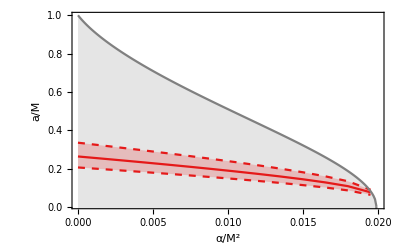

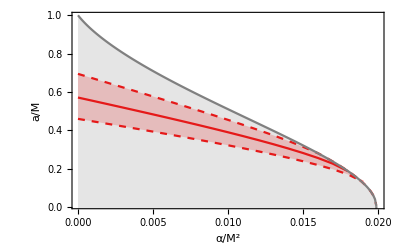

```mathematica
Show[f1,tik1,FrameLabel->{"α/M^2","a/M","Γ = 2","GRS1124-683"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[f2,tik1,FrameLabel->{"α/M^2","a/M","Γ = 5","GRS1124-683"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

```mathematica
(*Clear[q1,q2]*)
```

```mathematica
(*q1=Plot[{Aa2min[x],Aa2[x],Aa2max[x]},{x,10^-6,0.0154},Filling->{1->{3}},PlotStyle->{{Dashed,Red},Red,{Dashed,Red}},LabelStyle->Directive[Black,Bold],Frame->True,FrameLabel->{"α/M^2","a/M","GRS1124-683","Γ=2"}];*)
```

```mathematica
(*q2=Plot[{Aa5min[x],Aa5[x],Aa5max[x]},{x,10^-6,0.016},Filling->{1->{3}},PlotStyle->{{Dashed,Red},Red,{Dashed,Red}},LabelStyle->Directive[Black,Bold],Frame->True,FrameLabel->{"α/M^2","a/M","GRS1124-683","Γ=5"}];*)
```

## GROJ1655-40

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
Clear[P2,P5]
```

```mathematica
P2=70;P5=1600;
```

```mathematica
a2min[l_]:=a/.FindRoot[Log[P2]==LogK2min+2 Log[Wh[a,l]], {a,0.95-50.98 l}]//Quiet
a2[l_]:=a/.FindRoot[Log[P2]==LogK2+2 Log[Wh[a,l]], {a,0.86-35 l}]//Quiet
a2max[l_]:=a/.FindRoot[Log[P2]==LogK2max+2 Log[Wh[a,l]], {a,0.74-25 l}]//Quiet
```

```mathematica
data2min=ParallelTable[{l, a2min[l]}, {l, 0.00000000001,0.0038, 0.0002}];
data2=ParallelTable[{l, a2[l]}, {l, 0.00000000001,0.0112, 0.0002}];
data2max=ParallelTable[{l, a2max[l]}, {l, 0.00000000001,0.016, 0.0002}];
```

```mathematica
αc=0.00356;
d2minModified = Join[Select[data2min,First[#]≤αc&],Select[(*d5minAlt*)HH,First[#]>αc&]];
```

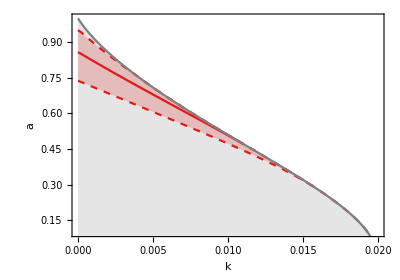

```mathematica
p1=ListPlot[{d2minModified,data2,data2max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,0.02},{0.1,1}},AspectRatio->0.7,PlotStyle->{{Red, Dashed},Red, {Red,Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
Show[{p1,tik1},FrameLabel->{"k","a", "Γ = 2", "GROJ1655-40"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

```mathematica
A5min[α_] := a/.FindRoot[Log[P5]==LogK5min + 2 Log[Wh[a,α]],{a,0.98-56.88 α}]//Quiet
A5[α_] := a/.FindRoot[Log[P5]==LogK5 + 2 Log[Wh[a,α]],{a,0.91-42.85 α}]//Quiet
A5max[α_] := a/.FindRoot[Log[P5]==LogK5max + 2 Log[Wh[a,α]],{a,0.8-32.2 α}]//Quiet
```

```mathematica
A5max[0.0002]
```

0.792771

```mathematica
(*data5min=ParallelTable[{l, A5min[l]}, {l, 0.00000000001,0.001, 0.0002}];
data5=ParallelTable[{l, A5[l]}, {l, 0.00000000001,0.0075, 0.0002}];
data5max=ParallelTable[{l, A5max[l]}, {l, 0.00000000001,0.008, 0.0002}];*)
```

```mathematica
data5min=ParallelTable[{l, A5min[l]}, {l, 0.00000000001,0.0009, 0.0002}];
data5=ParallelTable[{l, A5[l]}, {l, 0.00000000001,0.0072, 0.0002}];
data5max=ParallelTable[{l, A5max[l]}, {l, 0.00000000001,0.0142, 0.002}];
```

```mathematica
αc=0.000712;
d5minModified = Join[Select[data5min,First[#]≤αc&],Select[(*d5minAlt*)HH,First[#]>αc&]];
```

```mathematica
p2=ListPlot[{d5minModified,data5,data5max}, Joined->True, InterpolationOrder->1,PlotRange->{{0.,0.02},{0.1,1.01}},AspectRatio->0.7,  PlotStyle->{{Red, Dashed},Red, {Red, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
```

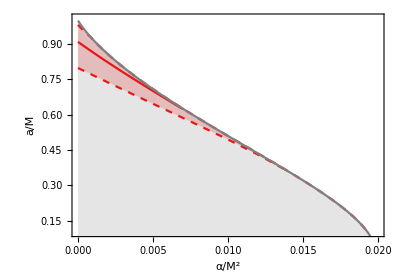

```mathematica
Show[{p2,tik1},FrameLabel->{"α/M^2","a/M", "Γ = 5", "GROJ1655-40"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## GRS 1915+105

```mathematica
Clear[P2,P5];
```

```mathematica
P2=42; P5=660;
```

```mathematica
Aa2min[α_] := a/.FindRoot[Log[P2]==LogK2min+2 Log[Wh[a,α]],{a,0.7}]//Quiet
Aa2[α_] := a/.FindRoot[Log[P2]==LogK2 + 2 Log[Wh[a,α]],{a,-27.4 α + 0.738}]//Quiet
Aa2max[α_] := a/.FindRoot[Log[P2]==LogK2max + 2 Log[Wh[a,α]],{a,-35.7 α + 0.859}]//Quiet
Aa5min[α_] := a/.FindRoot[Log[P5]==LogK5min + 2 Log[Wh[a,α]],{a,-31 α + 0.83}]//Quiet
Aa5[α_] := a/.FindRoot[Log[P5]==LogK5 + 2 Log[Wh[a,α]],{a,-24 α + 0.7055}]//Quiet
Aa5max[α_] := a/.FindRoot[Log[P5]==LogK5max + 2 Log[Wh[a,α]],{a,-19.5 α + 0.583}]//Quiet
```

```mathematica
d5max=ParallelTable[{α,Aa5max[α]},{α,0.000001,0.0185,0.0015}];
d5=ParallelTable[{α,Aa5[α]},{α,0.000001,0.017,0.0015}];
d5min=ParallelTable[{α,Aa5min[α]},{α,0.000001,0.013,0.0015}];
```

```mathematica
d2max=ParallelTable[{α,Aa2max[α]},{α,0.000001,0.018,0.001}];
d2=ParallelTable[{α,Aa2[α]},{α,0.000001,0.016,0.001}];
d2min=ParallelTable[{α,Aa2min[α]},{α,0.000001,0.011,0.0015}];
```

```mathematica
Aa5max[0.000001]
```

0.581244

```mathematica
Clear[f1,f2]
```

```mathematica
ListPlot[d1];
```

ListPlot::lpn: d1 is not a list of numbers or pairs of numbers.

```mathematica
αc=0.01195;
d5minModified = Join[Select[d5min,First[#]≤αc&],Select[(*d5minAlt*)HH,First[#]>αc&]];
```

```mathematica
f1=ListPlot[{d5max,d5,d5minModified},Joined->True, InterpolationOrder->1,PlotRange->{{0.,0.02},{0.1,0.9}},AspectRatio->0.7,PlotStyle->{{Red,Dashed},{Red},{Red,Dashed}},Frame->True,Filling->{1->{3}}];
```

```mathematica
αc=0.01045;
d2minModified = Join[Select[d2min,First[#]≤αc&],Select[(*d5minAlt*)HH,First[#]>αc&]];
```

```mathematica
f2=ListLinePlot[{d2max,d2,d2minModified},Joined->True, InterpolationOrder->1,PlotRange->{{0.,0.02},{0.1,0.9}},AspectRatio->0.7,PlotStyle->{{Red,Dashed},{Red},{Red,Dashed}},Frame->True,Filling->{1->{3}},Axes->False];
```

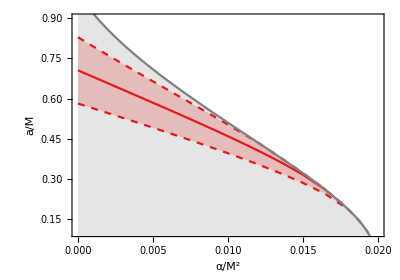

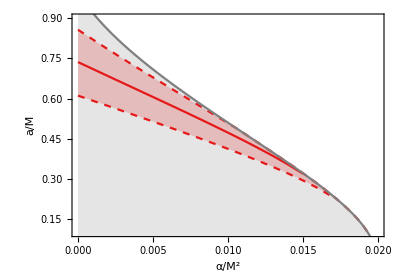

```mathematica
Show[f1,tik1,FrameLabel->{"α/M^2","a/M","Γ = 5","GRS 1915+105"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[f2,tik1,FrameLabel->{"α/M^2","a/M","Γ = 2","GRS 1915+105"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## Efficiency

### A0620-00

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
η1=0.054;η2=0.061;η3=0.07;
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,5},{a,0.2}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,5},{a,0.2}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&&1-Ene[r,a,l]==η3},{{r,6},{a,0.2}}]
```

```mathematica
dat1:=Table[{l,a2min[l]},{l,10^-6,2 10^-2,10^-3}];
dat2:=Table[{l,aa[l]},{l,10^-6,2 10^-2,10^-3}];
dat3:=Table[{l,amax[l]},{l,10^-6,2 10^-2,10^-3}];
```

```mathematica
a2min[0.01]
```

0.0456911

```mathematica
s1=Plot[{amin[l],aa[l],amax[l]},{l,0.000001,0.02},Filling->{1->{3}},PlotStyle->{{Blue,Dashed},Blue,{Blue,Dashed}},Frame->True,FrameLabel->{"α/M^2","a/M","A0620-00"},LabelStyle->Directive[Black,Bold],AxesLabel->None];
```

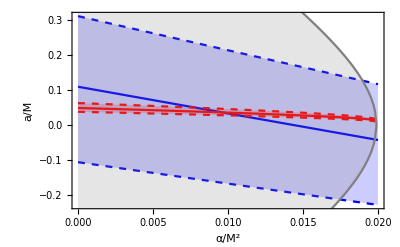

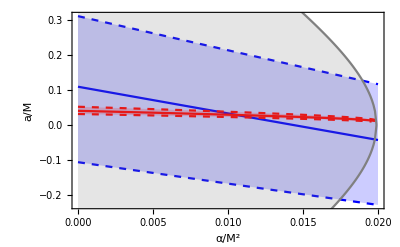

```mathematica
Show[s1,p1,tik1,FrameLabel->{"α/M^2","a/M","Γ = 2","A0620-00"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[s1,p2,tik1,FrameLabel->{"α/M^2","a/M","Γ = 5","A0620-00"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}](*with reg.Plot*)
```

### H1743-322

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
Clear[η1,η2,η3];
```

```mathematica
η1=0.065-0.011;η2=0.065;η3=0.065+0.017;
```

```mathematica
Clear[amin,aa,amax]
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,5.6},{a,0.3}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,5.6},{a,0.3}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η3},{{r,5.6},{a,0.3}}]//Quiet
```

```mathematica
s2=Plot[{amin[l],aa[l],amax[l]},{l,0.000001,0.02},Filling->{1->{3}},PlotStyle->{{Blue,Dashed},Blue,{Blue,Dashed}},Frame->True,FrameLabel->{"α/M^2","a/M","H1743-322"},LabelStyle->Directive[Black,Bold],AxesLabel->None];
```

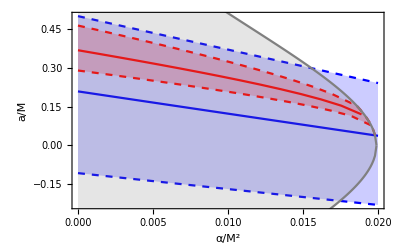

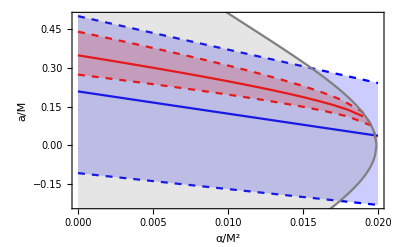

```mathematica
Show[s2,f1,tik1,FrameLabel->{"α/M^2","a/M","Γ=5","H1743-322"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[s2,f2,tik1,FrameLabel->{"α/M^2","a/M","Γ=2","H1743-322"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

### XTE J1550-564

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
Clear[η1,η2,η3];
```

```mathematica
η1=0.072-0.011;η2=0.072;η3=0.072+0.017;
```

```mathematica
Clear[amin,aa,amax];
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,5.6},{a,0.5}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,5.6},{a,0.5}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η3},{{r,5.6},{a,0.5}}]//Quiet
```

```mathematica
s3=Plot[{amin[l],aa[l],amax[l]},{l,0.000001,0.02},Filling->{1->{3}},PlotStyle->{{Blue,Dashed},Blue,{Blue,Dashed}},Frame->True,FrameLabel->{"α/M^2","a/M","XTEJ1550-564"},LabelStyle->Directive[Black,Bold],AxesLabel->None];
```

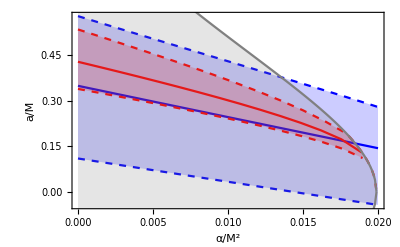

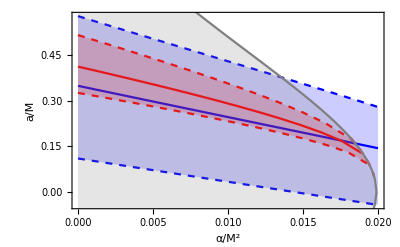

```mathematica
Show[s3,f1,tik1,FrameLabel->{"α/M^2","a/M","Γ = 2","XTEJ1550-564"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[s3,f2,tik1,FrameLabel->{"α/M^2","a/M","Γ = 5","XTEJ1550-564"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

### GRS1124-683

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
Clear[η1,η2,η3];
```

```mathematica
η1=0.095-0.017;η2=0.095;η3=0.095+0.025;
```

```mathematica
Clear[amin,aa,amax];
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,7},{a,0.8}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,5.5},{a,0.8}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η3},{{r,7},{a,0.8}}]//Quiet
```

```mathematica
s4=Plot[{amin[l],aa[l],amax[l]},{l,0.000001,0.02},Filling->{1->{3}},PlotStyle->{{Blue,Dashed},Blue,{Blue,Dashed}},PlotRange->{{10^-6,0.02},{0.,0.82}}, Frame->True,FrameLabel->{"α/M^2","a/M","GRS1124-683"},LabelStyle->Directive[Black,Bold],AxesLabel->None];
```

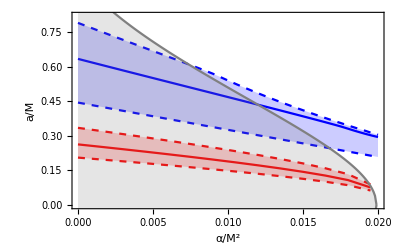

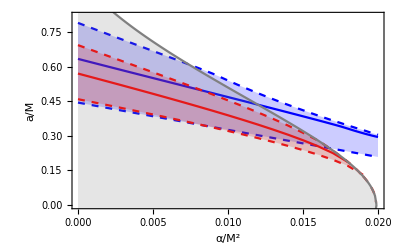

```mathematica
Show[s4,f1,tik1,FrameLabel->{"α/M^2","a/M","Γ = 2","GRS1124-683"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[s4,f2,tik1,FrameLabel->{"α/M^2","a/M","Γ = 5","GRS1124-683"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

### GROJ1655-40

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
Clear[η1,η2,η3];
```

```mathematica
η1=0.104-0.013;η2=0.104;η3=0.104+0.018;
```

```mathematica
Clear[amin,aa,amax];
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,6},{a,-24.02 l + 0.793}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,6},{a,-19.85 l + 0.706}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η3},{{r,6},{a,-24.972 l +0.8}}]//Quiet
```

```mathematica
ef1 = ParallelTable[{l,amin[l]},{l,10^-6,0.02,0.002}];
ef2 = ParallelTable[{l,aa[l]},{l,10^-6,0.02,0.002}];
ef3 = ParallelTable[{l,amax[l]},{l,10^-6,0.02,0.002}];
```

```mathematica
s5=ListLinePlot[{ef1,ef2,ef3},Joined->True, InterpolationOrder->1(*,PlotRange->{{0.,0.02},{0.1,1.01}}*),AspectRatio->0.7,  PlotStyle->{{Blue, Dashed},Blue, {Blue, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]];
```

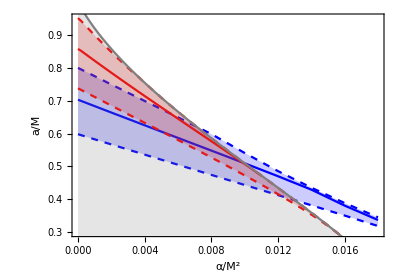

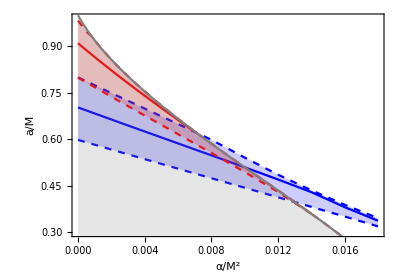

```mathematica
Show[{s5,p1,tik1},FrameLabel->{"α/M^2","a/M", "Γ = 2", "GROJ1655-40"},PlotRange->{{0,0.018},{0.3,0.95}},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[{s5,p2,tik1},FrameLabel->{"α/M^2","a/M", "Γ = 5", "GROJ1655-40"},PlotRange->{{0,0.018},{0.3,0.99}},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

### GRS 1915+105

```mathematica
Lr[r_,a_,α_]=D[L[r,a,α],r];
```

```mathematica
Clear[η1,η2,η3];
```

```mathematica
η1=0.234;η2=0.234+0.014;η3=0.234+0.028;
```

```mathematica
Clear[amin,aa,amax];
```

```mathematica
amin[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η1},{{r,6},{a,0.999}}]//Quiet
aa[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η2},{{r,6},{a,0.999}}]//Quiet
amax[l_]:=a/.FindRoot[{Lr[r,a,l]==0&& 1-Ene[r,a,l]==η3},{{r,6},{a,0.999}}]//Quiet
```

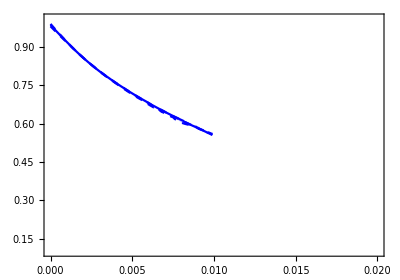

```mathematica
d1=ParallelTable[{l,amin[l]},{l,10^-6,0.01,0.0001}];
d2=ParallelTable[{l,aa[l]},{l,10^-6,0.01,0.0001}];
d3=ParallelTable[{l,amax[l]},{l,10^-6,0.01,0.0001}];
s6=ListLinePlot[{d1,d2,d3},Joined->True, InterpolationOrder->1,PlotRange->{{0.,0.02},{0.1,1.01}},AspectRatio->0.7,  PlotStyle->{{Blue, Dashed},Blue, {Blue, Dashed}}, Frame->True, Filling->{1->{3}}, Axes->False,LabelStyle->Directive[Black,Bold]]
```

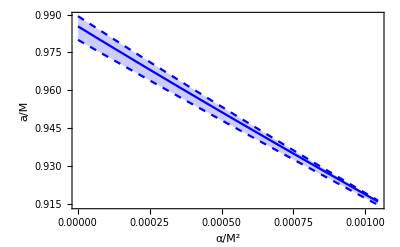

```mathematica
Plot[{amin[l],aa[l],amax[l]},{l,0.000001,0.001044},Filling->{1->{3}},PlotStyle->{{Blue,Dashed},Blue,{Blue,Dashed}},Frame->True,FrameLabel->{"α/M^2","a/M","GRS1915+105"},LabelStyle->Directive[Black,Bold],AxesLabel->None]
```

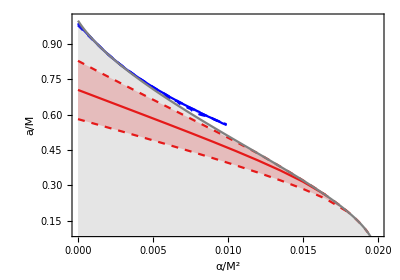

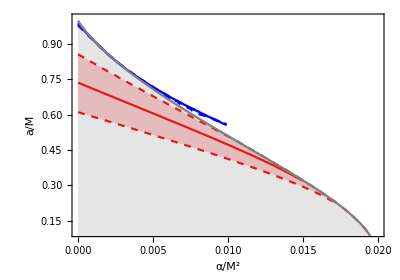

```mathematica
Show[s6,f1,tik1,FrameLabel->{"α/M^2","a/M","Γ = 5","GRS 1915+105"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
Show[s6,f2,tik1,FrameLabel->{"α/M^2","a/M","Γ = 2","GRS 1915+105"},LabelStyle->{FontFamily->"Times",Black,Italic,Bold}]
```

## veff(r) .

```mathematica
x = g44[r,a,α]/(g14[r,a,α]^2-g11[r,a,α] g44[r,a,α]);
y = g14[r,a,α]/(g14[r,a,α]^2-g11[r,a,α] g44[r,a,α]);
z = g11[r,a,α]/(g14[r,a,α]^2-g11[r,a,α] g44[r,a,α]);
```

```mathematica
A = (-g11[r,a,α])/g22[r,a,α] x^2-g44[r,a,α]/g22[r,a,α] y^2 + 2 g14[r,a,α]/g22[r,a,α] x y;
B = x L y g11[r,a,α]/g22[r,a,α] + y z L g44[r,a,α]/g22[r,a,α] - g14[r,a,α]/g22[r,a,α]*(x L z + y^2 L);
Csq = (-g44[r,a,α])/g22[r,a,α] L^2 z^2 + 2 g14[r,a,α]/g22[r,a,α] L^2 y z - 1/g22[r,a,α];
```

```mathematica
Vpl[r_,a_,α_,L_] = B/A + √(B^2 - A Csq);
```

```mathematica
Vmn[r_,a_,α_,L_] = B/A - √(B^2 - A Csq);
```

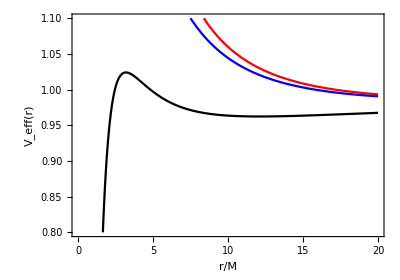

```mathematica
Plot[{Vpl[r,0,0.02,4],Vpl[r,0.8,0.012,6],Vpl[r,0.08,0.02,6]},{r,1.5,20},Frame->True,FrameLabel->{"r/M","V_eff(r)"},PlotStyle->{Black,Red,Blue},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotRange->{0.8,1.1},AspectRatio->0.7]
```

```mathematica
Limit[Vpl[r,a,α,L],r->Infinity]
```

1

```mathematica
Limit[Vmn[r,a,α,L],r->Infinity]
```

-1